# Weber Function

The Wikipedia page says to be cautious!
https://en.wikipedia.org/wiki/Weber_function
A google search
https://www.google.com/search?q=Computing+weber+functions
is useful.

```mathematica
?WeberE
```

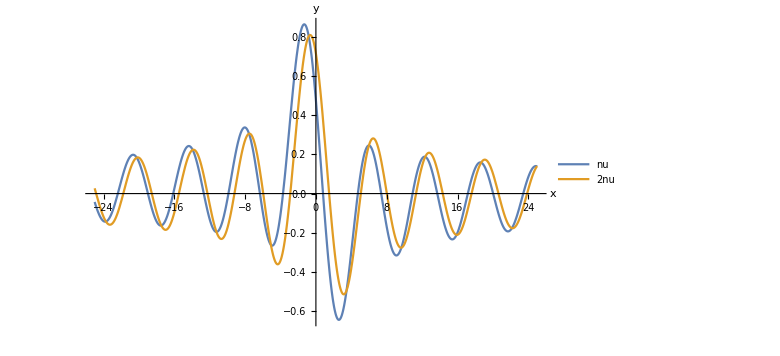

```mathematica
nu=0.333333;
Pic= Plot[{WeberE[nu,x],WeberE[2 nu,x]},{x,-25,25},
PlotLegends->{"nu","2nu"},
AxesLabel->{"x","y"}]
```

```mathematica
NSolve[ WeberE[nu,x]==0,x]
FindRoot[ WeberE[nu,x]==0,{x,0.6}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.804008}}

{x→0.804008}

```mathematica
{{x->0.8040083194854157}}
```

```mathematica
{x->0.8040083194854156}
```

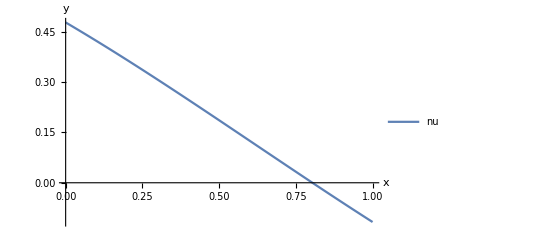

```mathematica
Plot[{WeberE[nu,x]},{x,0,1},
PlotLegends->{"nu","2nu"},
AxesLabel->{"x","y"}]
```

```mathematica
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\"]
Export["Test.png", Pic]
```

C:\Users\AllanStruthers\Desktop

Test.png

```mathematica
Plot3D[ Sin[x] Cos[x^2 -y], {x,-3,3},{y,-3,3},
PlotPoints->40,
RegionFunction->Function[{x,y}, x^2 + y^2 < 9]]
ContourPlot[ Sin[x] Cos[x^2 -y], {x,-3,3},{y,-3,3},
PlotPoints->40,
RegionFunction->Function[{x,y}, x^2 + y^2 < 9]]
```

-Graphics3D-

-Graphics-